Exercises for Section 11 | Strings and Text

Join two copies of the string "Hello". |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
StringJoin["Hello","Hello"]
```

HelloHello

Make a single string of the whole alphabet, in uppercase. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
StringJoin[ToUpperCase[Alphabet[]]]
```

ABCDEFGHIJKLMNOPQRSTUVWXYZ

Generate a string of the alphabet in reverse order. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
StringJoin[Reverse[Alphabet[]]]
```

zyxwvutsrqponmlkjihgfedcba

Join 100 copies of the string "AGCT". |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
StringJoin[Table["AGCT",100]]
```

AGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCT

Use StringTake, StringJoin and Alphabet to get "abcdef". |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
StringTake[StringJoin[Alphabet[]],6]
```

abcdef

Create a column with increasing numbers of letters from the string "this is about strings". |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Column[Table[StringTake["this is about strings",n],{n,1,21}]]
```

t
th
thi
this
this 
this i
this is
this is 
this is a
this is ab
this is abo
this is abou
this is about
this is about 
this is about s
this is about st
this is about str
this is about stri
this is about strin
this is about string
this is about strings

Make a bar chart of the lengths of the words in “A long time ago, in a galaxy far, far away”. |

EXPECTED OUTPUT »

-Graphics- | ×

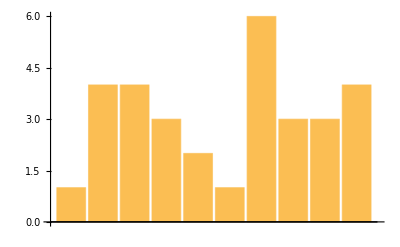

```mathematica
BarChart[StringLength[TextWords["A long time ago, in a galaxy far, far away"]]]
```

Find the string length of the Wikipedia article for “computer”. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
StringLength[WikipediaData["computer"]]
```

57705

Find how many words are in the Wikipedia article for “computer”. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Length[TextWords[WikipediaData["computer"]]]
```

8897

Find the first sentence in the Wikipedia article about “strings”. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
First[TextSentences[WikipediaData["strings"]]]
```

String or strings may refer to:

Make a string from the first letters of all sentences in the Wikipedia article about computers. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
StringJoin[StringTake[TextSentences[WikipediaData["computers"]],1]]
```

AMTATASCESEMTTTCTPP=ATTDBTTT==DTLTTTITIIMTTAAATTTIASIBIAITITIITS=CCATFTTTAEBNH=DHTTTTAB==BTDETTITIRT=PTEITDTTHACIINCTLOTIIIHBT==TTHTVTE=ECWATIHJTIIAAGTBAIT=TJFCJTHATHTTIWITT=TTDTKIHKNNHPNIMTGFTWISTIS=TTLTTTT=C=A=SH=TC==ATIET=WTTSC=TSC=TCATRDIRTPIWJSAIT=TES=TTSHTALTSG=AETTLSIETWOAMTTRACrRIIISFIIG=IDOHCIAMA=WTOBItSTBSIT=SMSTSS=SSCIW=T=TTMIAL=TITHTFMPWSTCBOTOI=ITTSTTITMWITC=PUTTS=MF=ATHHIT=PALTP=ETBOBSA=CTITTITCIIA"=AWA=TMH=TQCVSLTTT=ACARPE=AT====M

Find the maximum word length among English words from WordList[]. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Max[StringLength[WordList[]]]
```

23

Count the number of words in WordList[ ] that start with “q”. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Count[StringTake[WordList[],1],"q"]
```

194

Make a line plot of the lengths of the first 1000 words from WordList[]. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListLinePlot[StringLength[Take[WordList[],1000]]]
```

-Graphics-

Use StringJoin and Characters to make a word cloud of all letters in the words from WordList[]. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

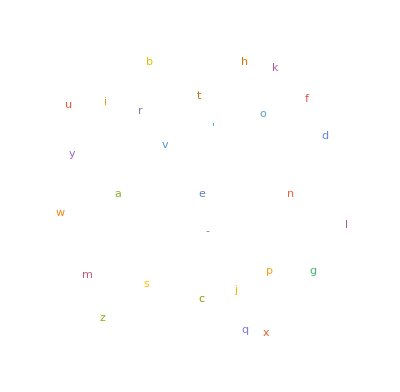

```mathematica
WordCloud[Characters[StringJoin[WordList[]]]]
```

Use StringReverse to make a word cloud of the last letters in the words from WordList[]. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

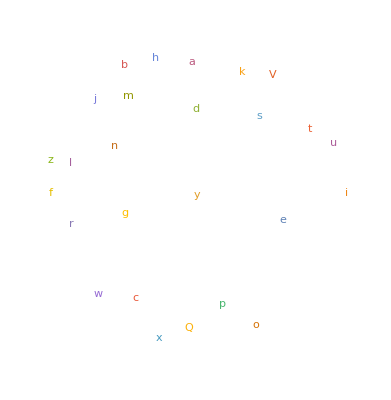

```mathematica
WordCloud[StringTake[StringReverse[WordList[]],1]]
```

Find the Roman numerals for the year 1959. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
RomanNumeral[1959]
```

MCMLIX

Find the maximum string length of any Roman-numeral year from 1 to 2020. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Max[StringLength[RomanNumeral[Table[year,{year,1,2020}]]]]
```

13

Make a word cloud from the first characters of the Roman numerals up to 100. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
WordCloud[StringTake[RomanNumeral[Table[n,{n,1,100}]],1]]
```

-Graphics-

Use Length to find the length of the Russian alphabet. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Length[Alphabet["Russian"]]
```

33

Generate the uppercase Greek alphabet. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ToUpperCase[Alphabet["Greek"]]
```

{Α,Β,Γ,Δ,Ε,Ζ,Η,Θ,Ι,Κ,Λ,Μ,Ν,Ξ,Ο,Π,Ρ,Σ,Τ,Υ,Φ,Χ,Ψ,Ω}

Make a bar chart of the letter numbers in “wolfram”. |

EXPECTED OUTPUT »

-Graphics- | ×

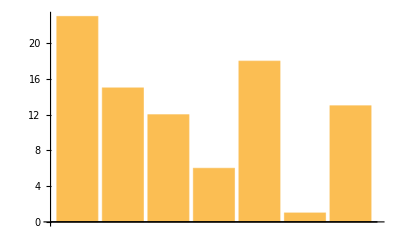

```mathematica
BarChart[LetterNumber["wolfram"]]
```

Use FromLetterNumber to make a string of 1000 random letters. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
StringJoin[FromLetterNumber[Table[RandomInteger[{1,26}],1000]]]
```

opvrqcqkrwpgtnhmeprvlpohpmmruqjqnmgclxsryalmhifbkjmrfzbzvumiytyowbjtthvqiemltnjylnftxwercttiaqastafhraktxolrdavflpuwgkqisqettxmtrdybejqxlxbyuzzsvmotrklaatjligobzjzyfdnmeaheynqqjlicwduiccmwrmwiqaxyoteuogvohflcgedjehackimyxndazcqfnuedmjemyvswhfuxwnsgauwkfbqgqrkbhzecdcbxoslydneooioleqhtmrmkjbdqaftbzosqamfnsamlzbsazdqjnulbxgdtkgbikwwrwsignpyfrlbmovcghlmyywoiksvfmbdflqtgqhtaslabzpmwpgdbmxbitmpxmtkvfazxnotmxnrksfbwgkzmwauytvssxcxlvusnlqbnbjwlsemhxxvmnbilntbfrfjdlqyjyudphnnmgyzuoyecoxwxyllgclxczkabmkawnvijocyronnpzsrgbbjydxcvhlllfumqvzdbgbtlqohehgsmtojzeujlamdytkulwfsdonkdprdefioqvtwlmfemwwpgpltddkzliaswevxpwmtojtdbgigenucciwlclhbzuoelpmgxctragyivbrmypkrmmgtnwxutvztemlpyzxaphjwswffsxdjcfiuxuxmetewjyfzbnwczrzulbgwwjjokracfzaygtjqhxbrqhahgkpdynndpmrxugbqfnrbxpoqjpzokhcgirbzopazoqrriwiublififzjgzanroxhzlceaqvhrfvsxqfnbrarlfbrcdfxjebrsfupqjqjatmkuligmeqnzhpwdzsdymvgwlwgiwtwexlsdkzqktyfkfinouemdtgsajbxulkyevbefumtyfrxdxtieycxtkrzfdcivdrqgysvuawscmdttlsyrrwolboczdfqbovmjojjivckyowxycxnuajgewzxvlars

Make a list of 100 random 5-letter strings. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Table[StringJoin[FromLetterNumber[Table[RandomInteger[{1,26}],5]]],100]
```

{hvciv,qogxl,ivodx,vaagn,ubahy,qfggz,qjpnp,uixzm,pvrpk,aptus,watzy,cfrst,qfprq,hoyuf,jepkc,xebcx,niseo,iredi,dqvjc,mdjcc,flunl,wclie,fvnkv,ygiah,yolvq,burzk,ggimo,jbdmk,mndgs,zwgby,fkbwb,kvdld,lhjso,dvbeg,pzzwa,uwugv,reowf,xnkve,pllzt,towyr,nixij,yxevt,uitoq,itdel,misvk,ckixm,omxzn,ckobg,znxkk,nxalm,lolyf,lpdvz,emymj,yznuy,hyxga,jycts,poqxy,brwdi,sqxgb,xhshl,apulk,yotdf,utoiq,xwfpu,shvyg,kffii,ufmef,relpe,bowfm,acshk,younc,trpfb,evpbi,etjxa,dswca,dktlp,msogd,bqyhk,locgu,tvdgb,rhjss,xyyhg,frwfj,szgab,dkjps,cuppd,bcjof,bswdf,yesko,asnkj,irpps,peqka,hfhit,ivwck,jrlct,iacms,hmslc,evtqs,rszku,jzuto}

Transliterate “wolfram” into Greek. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Transliterate["wolfram","Greek"]
```

βολφραμ

Get the Arabic alphabet and transliterate it into English. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Transliterate[Alphabet["Arabic"],"English"]
Transliterate[Alphabet["Arabic"]]
```

{ạ,b,t,tẖ,j,ḥ,kẖ,d,dẖ,r,z,s,sẖ,ṣ,ḍ,ṭ,ẓ,ʿ,gẖ,f,q,k,l,m,n,h,w,y}

{a,b,t,th,j,h,kh,d,dh,r,z,s,sh,s,d,t,z,ʿ,gh,f,q,k,l,m,n,h,w,y}

Make a white-on-black size-200 letter “A”. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ColorNegate[Rasterize[Style["A",200]]]
```

-Graphics-

Use Manipulate to make an interactive selector of size-100 characters from the alphabet, controlled by a slider. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Manipulate[Style[Take[Alphabet[],{n}],100],{n,1,26,1}];

Manipulate[Style[FromLetterNumber[n],100],{n,1,26,1}]
```

Use Manipulate to make an interactive selector of black-on-white outlines of rasterized size-100 characters from the alphabet, controlled by a menu. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Manipulate[ColorNegate[EdgeDetect[Rasterize[Style[n,100]]]],{n,Alphabet[]}]
```

Use Manipulate to create a “vision simulator” that blurs a size-200 letter “A” by an amount from 0 to 50. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Manipulate[Blur[Rasterize[Style["A",200]],b],{b,0,50}]
```

Generate a string of the alphabet followed by the alphabet written in reverse. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
StringJoin[Alphabet[],Reverse[Alphabet[]]]
```

abcdefghijklmnopqrstuvwxyzzyxwvutsrqponmlkjihgfedcba

Make a column of a string of the alphabet and its reverse. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Column[{StringJoin[Alphabet[]],StringJoin[Reverse[Alphabet[]]]}]
```

abcdefghijklmnopqrstuvwxyz
zyxwvutsrqponmlkjihgfedcba

Find how many sentences are in the Wikipedia article for “computer”. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Length[TextSentences[WikipediaData["computer"]]]
```

449

Join together without spaces, etc. the words in the first sentence in the Wikipedia article for “strings”. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
StringJoin[TextWords[Take[TextSentences[WikipediaData["strings"]],1]]]
StringJoin[TextWords[First[TextSentences[WikipediaData["strings"]]]]]
```

Stringorstringsmayreferto

Stringorstringsmayreferto

Find the length of the longest word in the Wikipedia article about computers. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Max[StringLength[TextWords[WikipediaData["computers"]]]]
```

25

Plot the lengths of Roman numerals for numbers up to 2000. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListLinePlot[StringLength[RomanNumeral[Table[n,{n,1,2000}]]]]
```

-Graphics-

Generate a string by joining the Roman numerals up to 100. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
StringJoin[RomanNumeral[Table[n,{n,1,100}]]]
```

IIIIIIIVVVIVIIVIIIIXXXIXIIXIIIXIVXVXVIXVIIXVIIIXIXXXXXIXXIIXXIIIXXIVXXVXXVIXXVIIXXVIIIXXIXXXXXXXIXXXIIXXXIIIXXXIVXXXVXXXVIXXXVIIXXXVIIIXXXIXXLXLIXLIIXLIIIXLIVXLVXLVIXLVIIXLVIIIXLIXLLILIILIIILIVLVLVILVIILVIIILIXLXLXILXIILXIIILXIVLXVLXVILXVIILXVIIILXIXLXXLXXILXXIILXXIIILXXIVLXXVLXXVILXXVIILXXVIIILXXIXLXXXLXXXILXXXIILXXXIIILXXXIVLXXXVLXXXVILXXXVIILXXXVIIILXXXIXXCXCIXCIIXCIIIXCIVXCVXCVIXCVIIXCVIIIXCIXC

Make a line plot of the successive letter numbers for the concatenation of all Roman numerals up to 30. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListLinePlot[LetterNumber[Characters[StringJoin[RomanNumeral[Table[n,{n,1,30}]]]]]]
```

-Graphics-

Find the maximum string length of the name of any integer up to 1000. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Max[StringLength[IntegerName[Table[RandomInteger[{1,1000}],100]]]]
```

27

Make a list of uppercase size-20 letters of the alphabet in random colors. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Table[Style[ToUpperCase[n],RandomColor[],20],{n,Alphabet[]}]
```

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z}

Make a list of 100 random 5-letter strings with the Russian alphabet. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Table[StringJoin[Table[Table[Take[Alphabet["Russian"],{RandomInteger[{1,33}]}],5],1]],100]
```

{тмщсг,исьмй,цакяё,жящкр,аэляз,щанхэ,эёшбь,ушорэ,сётуъ,ыькне,илъри,тцхгь,ейёво,лтхнф,мытзц,иичап,куцшм,ггтцб,цыопо,зоцбу,йагмэ,окхше,щжнящ,явйщт,сйомс,шьнцъ,ьшэхю,хзхэп,кяуют,окщюс,знуёз,срчпу,юамаа,эиюшт,фшйуз,нбчйг,мсиче,шкнщф,ючйъь,яиевж,пююдв,чцёёп,лцкчй,ьтюгы,вдмаъ,ьюодк,еуьвп,тьцпн,ыпукд,тюидя,ъюбчи,юющмщ,ядфпм,ишыан,шчуэй,зяббу,куюеи,абшюь,йзэтф,кутэц,ёйылз,екоъщ,твякд,быочэ,укюэс,ёъбюп,пёоэк,яясво,щъгйд,бзамэ,пещмш,ядтус,сщьжф,нъъня,яцтме,озхож,ётвеу,ицйиь,бфоъь,ажргж,ёакцл,щяьво,есхфс,шлкдч,цжажл,цуеий,жьжиш,юейщб,ухдшп,ъжёвр,мчыиг,деаёх,юнэев,нръдч,псфвг,ркясж,юиьна,унштъ,квфэл,янмсг}

Create a Manipulate to display edges in size-200 letter A, blurred from 0 to 50. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Manipulate[EdgeDetect[Blur[Rasterize[Style["A",200]],b]],{b,0,50}]
```

Add together white-on-black size-200 letters A and B. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ImageAdd[ColorNegate[Rasterize[Style["A",200]]],ColorNegate[Rasterize[Style["B",200]]]]
```

-Graphics-